```mathematica
SetDirectory["~/Projects/Paths/control/main/output/genf_z"];
```

```mathematica
inputs={Import["out_files"]}//Flatten;
pars=Import["pars.dat"]//Flatten;
results=Import["results.dat"];
meanSIM=Table[
{results[[i]][[3]],results[[i]][[4]]}
,{i,Length[results]}];
sim=ListLogLogPlot[meanSIM,Joined->True];
```

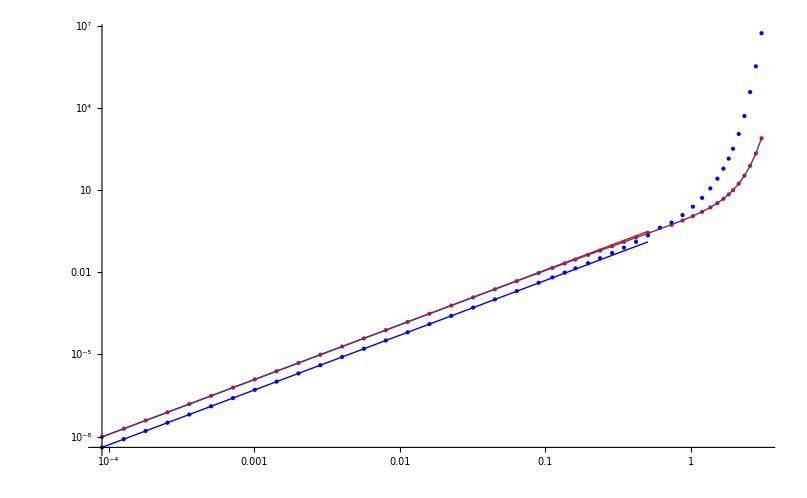

```mathematica
ClearAll;
Clear[cumsVSavjmp,plots];
cumsVSavjmp={};
plots={};
Do[
Clear[cums,mean,var];
cums={pars[[i]],mean,var};
data=Import[inputs[[i]]];
smin=First[data][[1]];
smax=Last[data][[1]];
genfexp=mean*s+1/2*var*s^2;
cumsVSavjmp=Append[cumsVSavjmp, cums/.FindFit[data,genfexp,{mean,var},s]];
plots=Append[plots,Show[ListPlot[data,Filling->Axis,Joined->True,PlotStyle->Red],Plot[genfexp,{s,smin,smax}]]];
,{i,Length[pars]}]
means=Table[{cumsVSavjmp[[i]][[1]],cumsVSavjmp[[i]][[2]]},{i,Length[cumsVSavjmp]}];
vars=Table[{cumsVSavjmp[[i]][[1]],cumsVSavjmp[[i]][[3]]},{i,Length[cumsVSavjmp]}];
points=ListLogLogPlot[{means,vars},PlotStyle->{Red,Blue}];
fits=LogLogPlot[{BesselJZero[0,1]/2*x^2,x^2/2},{x,pars[[1]],pars[[30]]},PlotStyle->{{Red,Thin},{Blue,Thin}}];
Show[{points,fits,sim}]
Export["meanANDvar.dat",cumsVSavjmp];
```

```mathematica
mλavj=Import["m_lambda_avjmp.dat"];
```

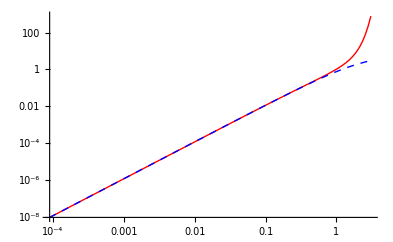

```mathematica
ClearAll[m,λ,c];
J0=BesselJ[0,λ];
J1=BesselJ[1,λ];
I0=BesselI[0,c];
I1=BesselI[1,c];
K0=BesselK[0,c];
K1=BesselK[1,c];
K2=BesselK[2,c];
avjz=2 λ/m^2(1+(λ J1 I0 + c J0 I1)/(c(J0^2+J1^2))( 2J0 K1 + λ J1 K1 - c J0 K2));
(*avjz=2 λ/m^2(1+(λ J1 I0 + c J0 I1)/(c(J0^2+J1^2))( J0 K1 + λ J1 K1 - c/2 J0 (K2+K0)));*)
pts=Table[
{2/m,avjz} /. {λ->mλavj[[i]][[2]], m->mλavj[[i]][[1]],c->Sqrt[(mλavj[[i]][[1]])^2-(mλavj[[i]][[2]])^2]}
,{i,Length[mλavj]}];
pts1=Table[
{2/m,(2λ)/m^2} /. {λ->mλavj[[i]][[2]], m->mλavj[[i]][[1]]}
,{i,Length[mλavj]}];
plotan=ListLogLogPlot[pts,Joined->True,PlotStyle->Red];
plotan1=ListLogLogPlot[pts1,Joined->True,PlotStyle->{Blue,Dashed}];
Show[plotan,plotan1]
```

```mathematica
ClearAll[avjz,m,λ,c];
J0=BesselJ[0,λ];
J1=BesselJ[1,λ];
I0=BesselI[0,c];
I1=BesselI[1,c];
K0=BesselK[0,c];
K1=BesselK[1,c];
K2=BesselK[2,c];
zgen=m^2/(m^2-s^2-2λ s)(1+2(λ J1 K0 - c J0 K1)/(J0^2+J1^2)( λ J1 I0 + c J0 I1)/(m^2-s^2-2 λ s))/.c->Sqrt[m^2-(λ+s)^2];
check=Table[
zgen/. {λ->mλavj[[i]][[2]], m->mλavj[[i]][[1]]},
{i,Length[mλavj]}];
plotchecks=Table[
Plot[Log[check[[i]]],{s,-Min[.1(-mλavj[[i]][[2]]+mλavj[[i]][[1]]),1],Min[.1(-mλavj[[i]][[2]]+mλavj[[i]][[1]]),1]}]
,{i,35}];
```